Thoughts:

List of rep rules vs complete input -> output map
e.g.
{a->b, bc->c}
vs
{aa->bb, ab->bb, ba->bb, ac

ok so rep rule is obviously better.

Find rep rule with <k rules

```mathematica
VisualizeSubstitutionSystem[rules_]:=Labeled[ResourceFunction["SubstitutionSystemCausalPlot"][ResourceFunction["SubstitutionSystemCausalEvolution"][#,"A",16],"ColorTable"->{Hue[0.06, 1, 1],Hue[0.73, 1, 1],Hue[0.14, 0.81, 0.99],Gray,RGBColor[0, 0.56, 1]}, ImageSize->{200, Automatic}], Text[#]]&[rules]
```

```mathematica
StringTuples=ResourceFunction["StringTuples"];
```

```mathematica
subs=StringTuples["abc", {1,3}]
```

{a,b,c,aa,ab,ac,ba,bb,bc,ca,cb,cc,aaa,aab,aac,aba,abb,abc,aca,acb,acc,baa,bab,bac,bba,bbb,bbc,bca,bcb,bcc,caa,cab,cac,cba,cbb,cbc,cca,ccb,ccc}

```mathematica
singlerules=SortBy[SortBy[Rule@@@Permutations[subs, {2}], Last], First]
```

```mathematica
AbsoluteTiming[Select[EchoFunction[ByteCount]@Subsets[singlerules, {2}], StringReplace[StringReplace[StringReplace["a",#], #], #]=="aa"&]]
```

333616064

{1.35553,{{a→ba,bba→aa},{a→ca,cca→aa}}}

```mathematica
singlerules[[#]]&/@ParallelSelect[EchoFunction[ByteCount]@Subsets[RandomSample[Range[Length[singlerules]], 200], {3}], MemberQ[{"aa", "aba", "aca", "aaa"},With[{rules=singlerules[[#]]},StringReplace[StringReplace[StringReplace[StringReplace[StringReplace["a", rules], rules], rules], rules],rules]]]&]
```

157608080

{{acb→aca,ccc→b,a→ac}}

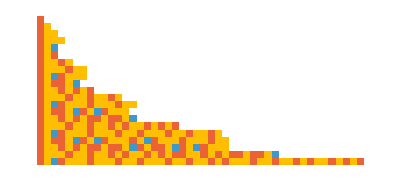
-Graphics-{acb→aca,ccc→b,a→ac}

```mathematica
ParallelMap[ClickToCopy[ArrayPlot[Replace[Characters/@SubstitutionSystem[#, "a", 20],{"a"->1, "b"->2, "c"->3}, All], ColorRules->"Colors", ImageSize->Full], #]&,]//Column
```

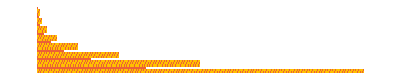

```mathematica
ArrayPlot[Replace[Characters/@SubstitutionSystem[#, "a", 30],{"a"->1, "b"->2, "c"->3}, All], ColorRules->"Colors"]&[{"acc"->"aa","ca"->"ac","a"->"cca"}]
```

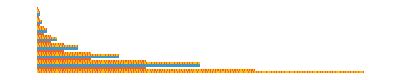

```mathematica
ArrayPlot[Replace[Characters/@SubstitutionSystem[#, "a", 30],{"a"->1, "b"->2, "c"->3}, All], ColorRules->"Colors"]&@{"a"->"ca","bbb"->"aa","cca"->"bbb"}
```

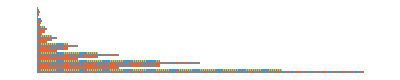

```mathematica
ArrayPlot[Replace[Characters/@SubstitutionSystem[#, "a", 30],{"a"->1, "b"->2, "c"->3}, All], ColorRules->"Colors"]&[{"cb"->"baa","a"->"bcb","baa"->"aa"}]
```

```mathematica
ArrayPlot[Replace[Characters/@SubstitutionSystem[#, "a", 200],{"a"->1, "b"->2, "c"->3}, All], ColorRules->"Colors"]&[{"accccccc"->"aa","ca"->"ac","a"->"cccccccca"}]
```

-Graphics-

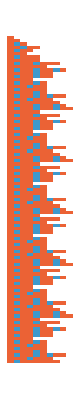

```mathematica
ArrayPlot[Replace[Characters/@SubstitutionSystem[#, "a", 100],{"a"->1, "b"->2, "c"->3}, All], ColorRules->"Colors"]&[{"aa"->"aba","baa"->"a","a"->"aa"}]
```

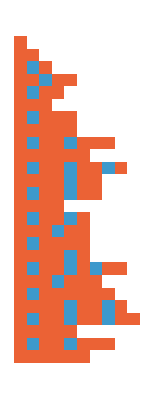
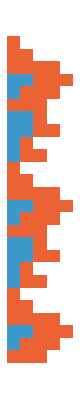
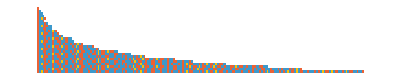

```mathematica
ArrayPlot[Replace[Characters/@SubstitutionSystem[Join[#, "a", 25],{"a"->1, "b"->2, "c"->3}, All], ColorRules->"Colors"]&/@
```

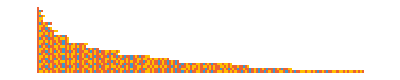
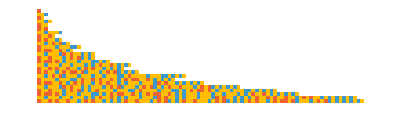
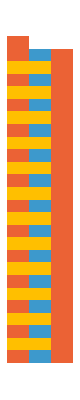
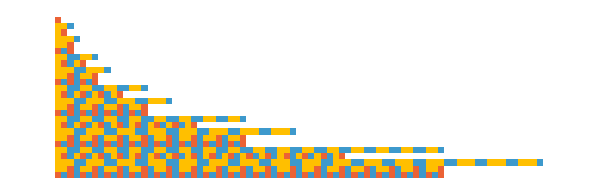
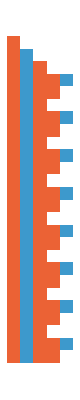
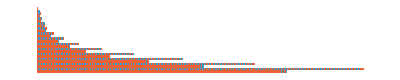
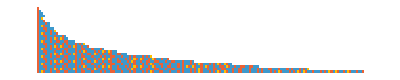

```mathematica
ArrayPlot[Replace[Characters/@SubstitutionSystem[#, "a", 25],{"a"->1, "b"->2, "c"->3}, All], ColorRules->"Colors"]&/@
```

```mathematica
SubstitutionSystem[{"cc"->"ac","acc"->"aaa","a"->"cc"}, "a", 20]
```

{a,cc,ac,ccc,acc,aaa,cccccc,acacac,ccccccccc,acacacacc,cccccccccaaa,acacacacccccccc,cccccccccaaaacacac,acacacaccccccccccccccccc,cccccccccaaaacacacacacacacc,acacacaccccccccccccccccccccccccccaaa,cccccccccaaaacacacacacacacacacacacaccccccc,acacacacccccccccccccccccccccccccccccccccccccccccaaaacacc,cccccccccaaaacacacacacacacacacacacacacacacacacacacccccccccccaaa,acacacaccccccccccccccccccccccccccccccccccccccccccccccccccccccccccccccaaaacacacacccccccc,cccccccccaaaacacacacacacacacacacacacacacacacacacacacacacacacacacacacacaccccccccccccccccaaaacacac}

```mathematica
Iconize[]
```